# SM + quadruplet

## Caption

This notebook provides examples illustrating the prediction of unitarity (UNI) and bounded-from-below (BFB) conditions using neural networks for an extension of the Standard Model with an additional 4-dimensional multiplet.
For further details regarding the model, see Refs. https://arxiv.org/abs/2404.07897 and https://arxiv.org/abs/2505.05272

## Initialization Code

Some useful definitions

```mathematica
compTarg="WVM";
compTarg="C";
```

Function for generation of parameters

```mathematica
Clear[genLambdasUNI4plet];
genLambdasUNI4plet=Compile[{},Module[{λ1,λ2,λ5,λ3,λ4},

λ1=RandomReal[{0,9}];
λ2=RandomReal[{0,10}];
λ3=RandomReal[{-9,9}];
λ4=RandomReal[{-16,16}];
λ5=RandomReal[{-11,8.5}];

{λ1,λ2,λ3,λ4,λ5}
],CompilationTarget->compTarg];
```

Function that selects data sets according to the UNI conditions

```mathematica
Clear[UniTest4plet];
UniTest4plet=Compile[{{data,_Real,1}},Module[{sqr2=Sqrt[2.],unBound=8.*Pi,unBnd=8.*Pi,
testUn1,testUn2,testUn3,testUn4,testUn5,testUn6,testUn7,testUn8,testUn9,test,test0,test1,test2,test3,test4,test5,test6,test7,test8,
λ1,λ2,λ3,λ4,λ5,λ6,λ7,λ8,ξ,λ1a,λ2a,λ4a,λ6a,l1,l2,l3,l4,l5,n,p,lmdT1,lmdT2,tabl0=Table[0.,{5}]},

testUn1=testUn2=testUn3=testUn4=testUn5=testUn6=testUn7=testUn8=testUn9=False;
test=test0=test1=test2=test3=test4=test5=test6=test7=test8=False;

{λ1,λ2,λ3,λ4,λ5}=data;
{λ1a,λ2a,λ4a}=Abs/@{λ1,λ2,λ4};
{l1,l2,l3,l4,l5}=data;
n=4; p=(n-1)/4; 

(*----------------------Uni1-------------------------*)
If[And[Abs[l1]<unBound,Abs[l2]<unBound,Abs[l3]+(n-1)/4*Abs[l4]<unBound,Abs[l3]+(n+1)/4*Abs[l4]<unBound],test1=True,Return[tabl0]];

(*----------------------Uni2-------------------------*)
If[And[Abs[l2+2*l5]<unBound,Abs[l2+3/5*l5]<unBound,Abs[l2+9/5*l5]<unBound],test2=True,Return[tabl0]];

(*----------------------Uni3-------------------------*)
lmdT1=-11/5*l5; lmdT2=3*l5;
If[And[Abs[l1+l2+lmdT1]+Sqrt[(l1-(l2+lmdT1))^2+1/6*n*(n^2-1)*l4^2]<2*unBound,
Abs[3*l1+(n+1)*l2+lmdT2]+Sqrt[(3*l1-((n+1)*l2+lmdT2))^2+8*n*l3^2]<2*unBound],test3=True,Return[tabl0]];

test=And[test1,test2,test3];
If[test,data,tabl0]

],CompilationTarget->compTarg];
```

Function that selects data sets according to the BFB conditions

```mathematica
Clear[BFBTest4plet];
BFBTest4plet=Compile[{{data,_Real,1}},Module[{sq2=Sqrt[2],unBnd=8*Pi,λ1,λ2,λ2p,λ3,λ4,λ5,λ1a,λ2a,λ4a,term1,term2,testUn1,testUn2,testUn3,testUn4,testUn5,testUn6,testUn7,testUn8,testUn9,test,test0,test1,test2,test3,test4,test5,test6,test7,test8,tabl0=Table[0.,{5}]},
test=test0=test1=test2=test3=test4=False;

testUn1=testUn2=testUn3=testUn4=testUn5=testUn6=testUn7=testUn8=testUn9=False;
test=test0=test1=test2=test3=test4=test5=test6=test7=test8=False;

{λ1,λ2,λ3,λ4,λ5}=data;
{λ1a,λ2a,λ4a}=Abs/@{λ1,λ2,λ4};


(*----------------------BFB1-------------------------*)
If[And[λ1>=0,λ2>=0,λ2+9/10*λ5>=0,λ3+√(λ1 λ2)-3/4 λ4a>=0,λ3+√(λ1 (λ2+9/10 λ5))>=0],test3=True,Return[tabl0]];

(*----------------------BFB2-------------------------*)
If[Or[λ5>-5/8 λ4^2/λ1,λ5>-5/6 √((λ2 λ4^2)/λ1),If[(8 λ5 λ1+5 λ4^2)/(80 λ5)<0,True,λ3+√(((9 λ5+10 λ2) (8 λ5 λ1+5 λ4^2))/(80 λ5))>0]],test4=True,Return[tabl0]];
data
],RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}, Parallelization->True,CompilationTarget->compTarg];
```

Function that selects data sets according to the UNI + BFB conditions

```mathematica
Clear[UniBFBTest4plet];
UniBFBTest4plet=Compile[{{data,_Real,1}},Module[{sq2=Sqrt[2],unBound=8*Pi,λ1,λ2,λ2p,λ3,λ4,λ5,λ1a,λ2a,λ4a,l1,l2,l3,l4,l5,lmdT1,lmdT2,n,p,term1,term2,testUn1,testUn2,testUn3,testUn4,testUn5,testUn6,testUn7,testUn8,testUn9,test,test0,test1,test2,test3,test4,test5,test6,test7,test8,tabl0=Table[0.,{5}]},
test=test0=test1=test2=test3=test4=False;

testUn1=testUn2=testUn3=testUn4=testUn5=testUn6=testUn7=testUn8=testUn9=False;
test=test0=test1=test2=test3=test4=test5=test6=test7=test8=False;

{λ1,λ2,λ3,λ4,λ5}=data;
{λ1a,λ2a,λ4a}=Abs/@{λ1,λ2,λ4};
{l1,l2,l3,l4,l5}=data;
n=4; p=(n-1)/4; 

(*----------------------Uni1-------------------------*)
If[And[Abs[l1]<unBound,Abs[l2]<unBound,Abs[l3]+(n-1)/4*Abs[l4]<unBound,Abs[l3]+(n+1)/4*Abs[l4]<unBound],test1=True,Return[tabl0]];

(*----------------------Uni2-------------------------*)
If[And[Abs[l2+2*l5]<unBound,Abs[l2+3/5*l5]<unBound,Abs[l2+9/5*l5]<unBound],test2=True,Return[tabl0]];

(*----------------------Uni3-------------------------*)
lmdT1=-11/5*l5; lmdT2=3*l5;
If[And[Abs[l1+l2+lmdT1]+Sqrt[(l1-(l2+lmdT1))^2+1/6*n*(n^2-1)*l4^2]<2*unBound,
Abs[3*l1+(n+1)*l2+lmdT2]+Sqrt[(3*l1-((n+1)*l2+lmdT2))^2+8*n*l3^2]<2*unBound],test3=True,Return[tabl0]];

(*----------------------BFB1-------------------------*)
If[And[λ1>=0,λ2>=0,λ2+9/10*λ5>=0,λ3+√(λ1 λ2)-3/4 λ4a>=0,λ3+√(λ1 (λ2+9/10 λ5))>=0],test3=True,Return[tabl0]];

(*----------------------BFB2-------------------------*)
If[Or[λ5>-5/8 λ4^2/λ1,λ5>-5/6 √((λ2 λ4^2)/λ1),If[(8 λ5 λ1+5 λ4^2)/(80 λ5)<0,True,λ3+√(((9 λ5+10 λ2) (8 λ5 λ1+5 λ4^2))/(80 λ5))>0]],test4=True,Return[tabl0]];
data
],RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}, Parallelization->True,CompilationTarget->compTarg];
```

Function that minimizes the potential V_4  in all directions of the real fields.

```mathematica
Clear[PotFunc4plet,Minim4pletFunc];
PotFunc4plet=Compile[{{param1,_Real,1},{param2,_Real,1}},Module[{λ1,λ2,λ3,λ4,λ5,λ6,c,d,e,f,g,h},

{λ1,λ2,λ3,λ4,λ5}=param1;
{c,d,e,f}=param2;

λ1/2+1/2 (c^2+d^2+e^2+f^2)^2 λ2+(c^2+d^2+e^2+f^2) λ3+1/4 (-3 c^2-d^2+e^2+3 f^2) λ4+1/5 (2 d^4+2 e^4-2 d e (3 c+2 √3 e) f+d^2 (-4 √3 c e+e^2+6 f^2)+c^2 (6 e^2+9 f^2)) λ5

],RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}(*, Parallelization->True*),CompilationTarget->compTarg];

Minim4pletFunc[parameters_]:=Module[{bndT=10^2,λ1,λ2,λ3,λ4,λ5,λ6,minFunc,minPotVal,c,d,e,f,g,h,parBounds,parRegion},

{λ1,λ2,λ3,λ4,λ5}=parameters;

parRegion={c,d,e,f};
parBounds=(-bndT≤#≤bndT)&/@parRegion;

minPotVal=NMinimize[{PotFunc4plet[{λ1,λ2,λ3,λ4,λ5},{c,d,e,f}],parBounds},parRegion,Method->{"NelderMead","RandomSeed"->RandomInteger[{1,1000}]}];
If[First[minPotVal]>0,
minPotVal=NMinimize[{PotFunc4plet[{λ1,λ2,λ3,λ4,λ5},{c,d,e,f}],parBounds},parRegion,Method->{"DifferentialEvolution","PostProcess"->{FindMinimum,Method->"PrincipalAxis"},"RandomSeed"->RandomInteger[{1,1000}],(*"SearchPoints"->100,*)"CrossProbability"->RandomReal[{0.5,0.9}],"ScalingFactor"->RandomReal[{0.5,0.9}]}]];

{First[minPotVal],parameters,parRegion}/.Last[minPotVal]

];
```

## Numerical computations

### Parameters of the potential

The datasets which obey only UNI conditions

```mathematica
zeroTabl=Table[0.,{5}]; 
valUNIlmd=ParallelTable[
valTMP=zeroTabl;
While[valTMP==zeroTabl,
pointRND=genLambdasUNI4plet[];
valTMP=UniTest4plet[pointRND];
];
valTMP
,{10^3}];//AbsoluteTiming
```

{0.052847,Null}

The datasets which obey UNI+BFB conditions

```mathematica
zeroTabl=Table[0.,{5}]; 
valUniBFBlmd=ParallelTable[
valTMP=zeroTabl;
While[valTMP==zeroTabl,
valTMP1=zeroTabl;
While[valTMP1==zeroTabl,
pointRND=genLambdasUNI4plet[];
valTMP1=UniTest4plet[pointRND];
];
valTMP=BFBTest4plet[pointRND];
];
valTMP
,{10^6}];//AbsoluteTiming
```

{4.8733,Null}

Lets  check computed datasets

```mathematica
DeleteCases[Table[UniBFBTest4plet[valUniBFBlmd[[x]]],{x,1,10^6}],zeroTabl]//Length
```

1000000

```mathematica
Export[NotebookDirectory[]<>"data/goodData_4plet.dat",valUniBFBlmd⟦;;⟧,"Data"]
```

The ranges of the parameters

```mathematica
lmdNames={"λ_1","λ_2","λ_3","λ_4","λ_5"};
TableForm[(MinMax/@Transpose@#),TableHeadings->{lmdNames,{"Min","Max"}}]&/@{valUniBFBlmd};
Grid[{%},Spacings->{3, 0}]
```

| Min | Max
λ_1 | 2.70068×10^-6 | 8.37746
λ_2 | 8.07419×10^-6 | 9.29771
λ_3 | -3.57177 | 8.63062
λ_4 | -12.0754 | 11.9525
λ_5 | -8.08579 | 8.26831

### Minimization of the potential V_4

Perform global minimization of the potential V_4 under various boundary conditions for the fields to find 1000 points which satisfy UNI and BFB conditions

```mathematica
zeroTabl=Table[0.,{5}];
minTestList=ParallelTable[
minPotVal1=-1;
While[minPotVal1<0,
valTMP=zeroTabl;
While[valTMP==zeroTabl,
lmdT=genLambdasUNI4plet[];
valTMP=UniTest4plet[lmdT];
];
(minPotVal=Minim4pletFunc[valTMP])//Quiet;
minPotVal1=First@minPotVal;
];
minPotVal
,{1000}];//AbsoluteTiming
```

{53.2208,Null}

Let’s  check computed datasets

```mathematica
DeleteCases[UniTest4plet/@minTestList⟦;;,2⟧,zeroTabl]//Length
DeleteCases[UniBFBTest4plet[#]&/@minTestList⟦;;,2⟧,zeroTabl]//Length
```

1000

1000

## Nets training

### Training data

generation of raw  data

```mathematica
zeroTabl=Table[0.,{5}];
dataT107=ParallelTable[
pointRND=genLambdasUNI4plet[];
valTMP=If[UniBFBTest4plet[pointRND]==zeroTabl,0,1];
pointRND->valTMP
,{10^7}];//AbsoluteTiming
```

{18.1919,Null}

points which obey UNI+BFB conditions in raw data

```mathematica
Count[dataT107⟦;;,2⟧,1]
%/Length[dataT107]*100//N
```

221028

2.21028

loading  dataset with “good” data, which obey UNI+BFB conditions generated previously

```mathematica
valUniBFBlmd=ToExpression@Import[NotebookDirectory[]<>"data/goodData_4plet.dat","Data"];
```

```mathematica
badDataG=Select[dataT107,#⟦2⟧==0&]⟦;;,1⟧;
%//Length
goodDataG=valUniBFBlmd;
```

9778972

trainingData with 10% of good points. Such combination is the most effective to train the first net.

```mathematica
trainingData=RandomSample@Join[Rule[#,0]&/@badDataG⟦;;⟧,Rule[#,1]&/@goodDataG⟦;;⟧];
Count[trainingData⟦;;,2⟧,1]
%/Length[dataT107]*100//N
```

1000000

10.

definition of decoder

```mathematica
dec=NetDecoder[{"Class",{0,1}}];
```

### net-1 (128 neurons)

definition  of net-1

```mathematica
netOne=NetInitialize[NetChain[{128,Ramp,128,Ramp,128,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->5],Method->{"Xavier","FactorType"->"Mean"}];
```

training of net-1 with trainingData dataset

```mathematica
trainPart=IntegerPart[Length[trainingData]*0.9];
timeStart=AbsoluteTime[];
trainedNet1=NetTrain[netOne,trainingData⟦;;trainPart⟧,BatchSize->2^14,ValidationSet->trainingData⟦trainPart;;⟧,TargetDevice->"GPU",Method->"RMSProp",(*WorkingPrecision->"Real32"*)WorkingPrecision->"Mixed",MaxTrainingRounds->500(*,LearningRate->0.00025*)];
AbsoluteTime[]-timeStart
```

603.805046

```mathematica
Export[NotebookDirectory[]<>"data/networks/trainedNet1_4plet.wlnet",trainedNet1]
```

### net-2 (256 neurons)

definition  of net-2

```mathematica
netTwo=NetInitialize[NetChain[{256,Ramp,256,Ramp,256,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->5],Method->{"Xavier","FactorType"->"Mean"}];
```

let’s make trainingDataNet1 using net-1

```mathematica
zeroTabl=Table[0.,{5}];
dataTT=ParallelTable[
dataT=Table[genLambdasUNI4plet[],{10^6}];
results=trainedNet1[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[UniBFBTest4plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{3*45}];//AbsoluteTiming
```

{34.1284,Null}

let’s  check the ratio of good points

```mathematica
trainingDataNet1=Flatten[dataTT,1];
%//Length
Count[trainingDataNet1⟦;;,2⟧,1]
Count[trainingDataNet1⟦;;,2⟧,1]/Length[trainingDataNet1]//N
```

3024387

2983770

0.98657

we dilute the trainingDataNet1 dataset  to reduce the percentage of good points, if necessary.

```mathematica
trainingDataNet2=RandomSample@Join[Rule[#,0]&/@badDataG,trainingDataNet1];
%//Length
Count[trainingDataNet2⟦;;,2⟧,1]
%/Length[trainingDataNet2]//N
trainPart=IntegerPart[Length[trainingDataNet2]*0.9]
```

12803359

2983770

0.233046

11523023

training of net-2 with trainingDataNet2 dataset

```mathematica
timeStart=AbsoluteTime[];
trainedNet2=NetTrain[netTwo,trainingDataNet2⟦;;trainPart⟧,BatchSize->2^14,ValidationSet->trainingDataNet2⟦trainPart;;⟧,TargetDevice->"GPU",Method->"RMSProp",WorkingPrecision->"Mixed",MaxTrainingRounds->500];
AbsoluteTime[]-timeStart
```

935.618516

```mathematica
Export[NotebookDirectory[]<>"data/networks/trainedNet2_4plet.wlnet",trainedNet2]
```

### net-3 (512 neurons)

definition  of net-3

```mathematica
netThree=NetInitialize[NetChain[{512,Ramp,512,Ramp,512,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->5],Method->{"Xavier","FactorType"->"Mean"}];
```

training of net-3 with trainingDataNet2 dataset

```mathematica
timeStart=AbsoluteTime[];
trainedNet3=NetTrain[netThree,trainingDataNet2⟦;;trainPart⟧,BatchSize->2^14,ValidationSet->trainingDataNet2⟦trainPart;;⟧,TargetDevice->"GPU",Method->"RMSProp",WorkingPrecision->"Mixed",MaxTrainingRounds->500];
AbsoluteTime[]-timeStart
```

1647.40081

```mathematica
Export[NotebookDirectory[]<>"data/networks/trainedNet3_4plet.wlnet",trainedNet3]
```

prediction of UNI+ BFB conditions with net-3

```mathematica
zeroTabl=Table[0.,{5}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI4plet[],{10^6}];
results=trainedNet3[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[UniBFBTest4plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{45}];//AbsoluteTiming
```

{45.1936,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

1003367

995893

0.992551

### net-4 (1024 neurons)

definition  of net-4

```mathematica
netFour=NetInitialize[NetChain[{1024,Ramp,1024,Ramp,1024,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->5],Method->{"Xavier","FactorType"->"Mean"}];
```

training of net-4 with trainingDataNet2 dataset

```mathematica
timeStart=AbsoluteTime[];
trainedNet4=NetTrain[netFour,trainingDataNet2⟦;;trainPart⟧,BatchSize->2^14,ValidationSet->trainingDataNet2⟦trainPart;;⟧,TargetDevice->"GPU",Method->"RMSProp",WorkingPrecision->"Mixed",MaxTrainingRounds->500];
AbsoluteTime[]-timeStart
```

3625.306666

```mathematica
Export[NotebookDirectory[]<>"data/networks/trainedNet4_4plet.wlnet",trainedNet4]
```

prediction of UNI+ BFB conditions with net-4

```mathematica
zeroTabl=Table[0.,{5}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI4plet[],{10^6}];
results=trainedNet4[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[UniBFBTest4plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{45}];//AbsoluteTiming
```

{162.274,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

999117

993122

0.994

## Nets testing

Predictions of net-1

```mathematica
zeroTabl=Table[0.,{5}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI4plet[],{10^6}];
results=trainedNet1[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[UniBFBTest4plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{45}];//AbsoluteTiming
```

{12.4292,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

1009357

995979

0.986746

Predictions of net-2

```mathematica
zeroTabl=Table[0.,{5}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI4plet[],{10^6}];
results=trainedNet2[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[UniBFBTest4plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{45}];//AbsoluteTiming
```

{19.5873,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

1005002

995671

0.990715

Predictions from the combination of net-1 and net-2

```mathematica
zeroTabl=Table[0.,{5}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI4plet[],{10^6}];
results=trainedNet1[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
results=trainedNet2[results2⟦;;,1⟧];
results2=DeleteCases[Thread[results2⟦;;,1⟧->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
If[UniBFBTest4plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{45}];//AbsoluteTiming
```

{13.5887,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

996141

992429

0.996274

Predictions from the combination of net-2, net-3, and net-4

```mathematica
zeroTabl=Table[0.,{5}]; 
dataTT=ParallelTable[
dataT=Table[genLambdasUNI4plet[],{10^6}];
results=trainedNet2[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
results=trainedNet3[results2⟦;;,1⟧];
results2=DeleteCases[Thread[results2⟦;;,1⟧->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
results=trainedNet4[results2⟦;;,1⟧];
results2=DeleteCases[Thread[results2⟦;;,1⟧->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
If[UniBFBTest4plet[#]==zeroTabl,#->0,#->1]&/@results2⟦;;,1⟧
,{45}];//AbsoluteTiming
```

{24.845,Null}

Let us examine the fraction of valid points in the dataset.

```mathematica
dataT3=Flatten[dataTT,1];
%//Length
Count[dataT3⟦;;,2⟧,1]
%/Length[dataT3]//N
```

992694

990813

0.998105

Predictions from the combination of net-2, net-3, and net-4 with validation performed by potential minimization

Here, we compute from the raw data using net-2 through net-4, with validation performed by potential minimization. A total of approximately 1000 good points are evaluated.

```mathematica
timeStart=AbsoluteTime[];
zeroTabl=Table[0.,{5}];
dataTT=ParallelTable[
dataT=Table[genLambdasUNI4plet[],{10^4}];
results=trainedNet2[dataT];
results2=DeleteCases[Thread[dataT->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
results=trainedNet3[results2⟦;;,1⟧];
results2=DeleteCases[Thread[results2⟦;;,1⟧->results],_->0];
If[Length[results2]==0,results2={zeroTabl->0}];
results=trainedNet4[results2⟦;;,1⟧];
results2=DeleteCases[Thread[results2⟦;;,1⟧->results],_->0]
,{5}];//AbsoluteTiming

dataT3=DeleteCases[Flatten[dataTT],zeroTabl->_];
tmp=DeleteCases[UniBFBTest4plet/@dataT3[[;;,1]],zeroTabl]//Length;
{Length[dataT3],tmp,tmp/Length[dataT3]//N}

minTestList=ParallelTable[
(minPotVal=Minim4pletFunc[dataT3[[xx,1]]])//Quiet;
minPotVal
,{xx,1,Length[dataT3]}];//AbsoluteTiming
minTestList=DeleteCases[minTestList,{a_/;a<0,_,_}];
%//Length
AbsoluteTime[]-timeStart
```

{0.120683,Null}

{1089,1086,0.997245}

{19.2581,Null}

1088

19.38467

Let us examine the fraction of valid points in the dataset.

```mathematica
DeleteCases[UniBFBTest4plet/@minTestList[[;;,2]],zeroTabl]//Length
%/Length[minTestList]//N
```

1086

0.998162

Classifier Measurements of nets

```mathematica
zeroTabl=Table[0.,{5}];
dataT=ParallelTable[
pointRND=genLambdasUNI4plet[];
valTMP=If[UniBFBTest4plet[pointRND]==zeroTabl,0,1];
pointRND->valTMP
,{10^7}];//AbsoluteTiming
```

{18.1457,Null}

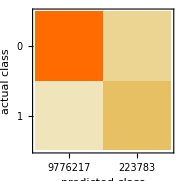
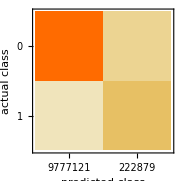
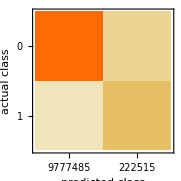
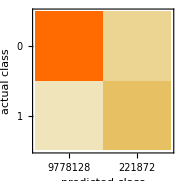
{Classifier Measurements
Classifier method | Net
Number of test examples | 10000000
Accuracy | (99.96290.0006) %
Accuracy baseline | (97.7860.005) %
Geometric mean of probabilities | 0.999 ± 0.000012
Mean cross entropy | 0.000877 ± 0.000012
Single evaluation time | 3.28 ms/example
Batch evaluation speed | 793. examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 10000000
Accuracy | (99.97400.0005) %
Accuracy baseline | (97.7860.005) %
Geometric mean of probabilities | 0.999 ± 0.000011
Mean cross entropy | 0.000664 ± 0.000011
Single evaluation time | 2.89 ms/example
Batch evaluation speed | 793. examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 10000000
Accuracy | (99.97710.0005) %
Accuracy baseline | (97.7860.005) %
Geometric mean of probabilities | 0.999 ± 8.9×10^-6
Mean cross entropy | 0.000554 ± 8.9×10^-6
Single evaluation time | 3.89 ms/example
Batch evaluation speed | 258. examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 10000000
Accuracy | (99.97840.0005) %
Accuracy baseline | (97.7860.005) %
Geometric mean of probabilities | 0.999 ± 9.×10^-6
Mean cross entropy | 0.000543 ± 9.×10^-6
Single evaluation time | 3.45 ms/example
Batch evaluation speed | 110. examples/ms
-Graphics- | }

```mathematica
classfT=ClassifierMeasurements[#,RandomSample[dataT]⟦;;⟧]&/@{trainedNet1,trainedNet2,trainedNet3,trainedNet4}
```